```mathematica
Quit[]
```

```mathematica
Needs["FeynArts`"]
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/TopEFT-UFO/TopEFT-UFO",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

generic model {../Models/TopEFT-UFO/TopEFT-UFO} initialized

classes model {../Models/TopEFT-UFO/TopEFT-UFO} initialized

in total: 1 Particles insertion

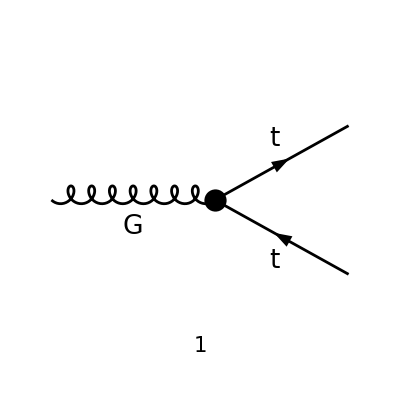

```mathematica
tops = CreateTopologies[0,1->2];
processGGT =  { V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},GenericModel->"../Models/TopEFT-UFO/TopEFT-UFO"];
Paint[allDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]
```

in total: 1 Particles amplitude

FeynAmpList(Process→(V(4,{Glu1}) | p1 | 0 | {})→(F(9,{Col2}) | k1 | MT | {(2 Q)/3}
-F(9,{Col3}) | k2 | MT | {-(2 Q)/3}),Model→{../Models/TopEFT-UFO/TopEFT-UFO},GenericModel→{../Models/TopEFT-UFO/TopEFT-UFO},AmplitudeLevel→{Particles},ExcludeParticles→{S(1)},ExcludeFieldPoints→{},LastSelections→{})(FeynAmp(GraphID(Topology==1,Generic==1,Particles==1,Number==1),Integral[],SumOver(Col2,3,External) SumOver(Col3,3,External) SumOver(Glu1,8,External) (-((ⅈ C1 GS yDM^2 (p1)(Lor1) SUNT(Glu1,Col2,Col3) gs(-(k1)).(omSubscript[+]))/(32 π^2)+(ⅈ C1 GS yDM^2 (p1)(Lor1) SUNT(Glu1,Col2,Col3) gs(-(k2)).(omSubscript[+]))/(32 π^2)+(ⅈ C1 GS yDM^2 (-(k2))(Lor1) SUNT(Glu1,Col2,Col3) gs(-(k1)).(omSubscript[+]))/(32 π^2)+(ⅈ C1 GS yDM^2 (-(k1))(Lor1) SUNT(Glu1,Col2,Col3) gs(-(k2)).(omSubscript[+]))/(32 π^2)+(ⅈ C12 GS yDM^2 (p1)(Lor1) SUNT(Glu1,Col2,Col3) gs(p1).(omSubscript[+]))/(96 π^2)+ⅈ gc91L SUNT(Glu1,Col2,Col3) ga(Lor1).(omSubscript[-])-(ⅈ C1 GS yDM^2 (-(k1)).(-(k1)) SUNT(Glu1,Col2,Col3) ga(Lor1).(omSubscript[+]))/(32 π^2)-(ⅈ C1 GS yDM^2 (-(k2)).(-(k2)) SUNT(Glu1,Col2,Col3) ga(Lor1).(omSubscript[+]))/(32 π^2)-(ⅈ C12 GS yDM^2 (p1).(p1) SUNT(Glu1,Col2,Col3) ga(Lor1).(omSubscript[+]))/(96 π^2)+ⅈ gc91R SUNT(Glu1,Col2,Col3) ga(Lor1).(omSubscript[+])))))